# Power Grid Stability Analysis

## Eigenvalue Analysis of Nordic Power Grid Frequency Dynamics

## Initializations

#### Global Values

For accurate font size in graphs.

```mathematica
cm=Quantity[1,"Centimeters"]/(Quantity[1,"Inches"]/72)//N;
```

Here we find and start an external evaluation session with a local python kernel.

#### Load Data

```mathematica
aList=Import[NotebookDirectory[]<>"aList.m"];
```

```mathematica
bList=Import[NotebookDirectory[]<>"bList.m"];
```

```mathematica
cList=Import[NotebookDirectory[]<>"cList.m"];
```

#### Core Stability Analysis function

Find number of fixed points (numeric solution), their values, and eigenvalues of the linearized system on each fixed point.
Fixed points are grouped in stable and unstable groups.

```mathematica
NFixedPointsAndEigenValuesComplete[FixedPointEquations_,JacobianEquations_,n_]:=(Module[{FixedPoints,FixedPointsRules,EigenValues,StableFixedPointIndicies,UnStableFixedPointIndicies},
(*Eigenvalues sorts the eigenvalues in an desending order of their absolute values*)

FixedPointsRules=NSolve[FixedPointEquations,Table[Indexed[x,i],{i,1,n}],Reals];
FixedPoints=Table[Indexed[x,i],{i,1,n}]/.FixedPointsRules;
EigenValues=Map[Eigenvalues][JacobianEquations/.FixedPointsRules];
StableFixedPointIndicies=Position[Re[EigenValues],__?(Apply[And,Map[(#<0&),#],{0}]&),1];
UnStableFixedPointIndicies=Position[Re[EigenValues],__?(Apply[Or,Map[(#≥0&),#],{0}]&),1];
{{Length[FixedPoints],EigenValues,FixedPoints},{Length[Extract[FixedPoints,StableFixedPointIndicies]],Extract[EigenValues,StableFixedPointIndicies],Extract[FixedPoints,StableFixedPointIndicies]},{Length[Extract[FixedPoints,UnStableFixedPointIndicies]],Extract[EigenValues,UnStableFixedPointIndicies],Extract[FixedPoints,UnStableFixedPointIndicies]}}

]
)
(*This is changed to get n*)
```

## Fixed Points & Eigen Values Computation

### Evaluate list of dynamical equations and Jacobians for all windows

```mathematica
FixedPointEquationsWin=With[{n=7},Table[Table[Sum[aList[[l]][[i,j]]Indexed[x,j],{j,1,n}]+ Sum[bList[[l]][[i,j,k]]Indexed[x,j] Indexed[x,k],{j,1,n},{k,1,n}]+ Sum[cList[[l]][[i,j,k,s]]Indexed[x,j] Indexed[x,k] Indexed[x,s],{j,1,n},{k,1,n},{s,1,n}]==0,{i,1,n}],{l,1,240}]];
```

```mathematica
JacobianEquationsWin=With[{n=7},Table[D[Table[Sum[aList[[l]][[i,j]]Indexed[x,j],{j,1,n}]+ Sum[bList[[l]][[i,j,k]]Indexed[x,j] Indexed[x,k],{j,1,n},{k,1,n}]+ Sum[cList[[l]][[i,j,k,s]]Indexed[x,j] Indexed[x,k] Indexed[x,s],{j,1,n},{k,1,n},{s,1,n}],{i,1,n}],{Table[Indexed[x,i],{i,1,n,1}]}],{l,1,240}]];
```

Evaluation of fixed points and eigenvalues

```mathematica
FixedPointsWindows=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],7])&[Floor@l],{l,1,240}];(*(~1d run time)*)
```

Reading Stability Data:

```mathematica
FixedPointsWindows=Import[NotebookDirectory[]<>"AllWindowsFixedPoints.m"];
```

We choose the fixed point which stays closest to mean x_i = 0 through time.

```mathematica
chosenFixedPointValues=FixedPointsWindows[[;;,2,3,-1]];
```

```mathematica
chosenFixedPointValueRules=Table[Table[Indexed[x,i]->chosenFixedPointValues[[w,i]],{i,1,7}],{w,1,240}];
```

List of  for all windows

```mathematica
effectiveAdjacencies=Table[(JacobianEquationsWin[[w]]/.chosenFixedPointValueRules[[w]]),{w,1,240}];
```

Eigenvectors of the fixed point

```mathematica
chosenFixedPointEigenvectors=Map[Eigenvectors][effectiveAdjacencies];(*Eigenvectors with numeric eigenvalues are sorted in order of decreasing absolute value of their eigenvalues*)
```

```mathematica
rightmostEigenvecLargestIndexe=Flatten[(Position[#,Max[#]]&)/@Abs@chosenFixedPointEigenvectors[[;;,-1]]]
```

{}

```mathematica
leftmostEigenvecLargestIndexe=Flatten[(Position[#,Max[#]]&)/@Abs@chosenFixedPointEigenvectors[[;;,1]]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,7,7,7,7,7,7,7,7}

### Figures

#### Fig. 3. (G)

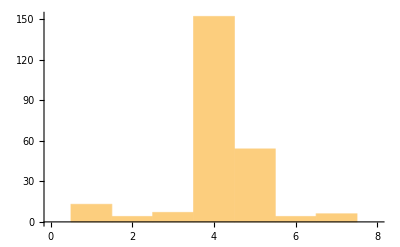

```mathematica
Histogram[rightmostEigenvecLargestIndex,{1},PlotRange->{{0,8},Automatic}]
```

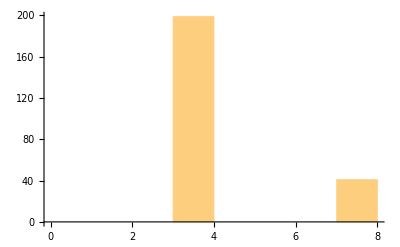

```mathematica
Histogram[leftmostEigenvecLargestIndex,{1},PlotRange->{{0,8},All}]
```

#### Fig. S4.

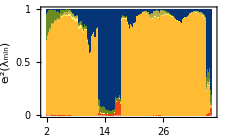

```mathematica
eigenVecFigLeft=BarChart[(Map[(#^2&),(Abs@chosenFixedPointEigenvectors),{2}][[;;,1]]),
Frame->True,
Axes->False,

FrameTicks->{{(*Automatic*){0,0.5,1},None},{Table[{((i-2)/34*239)+1,i},{i,Range[2,36,4]}],None}},


FrameTicksStyle->Directive[Black,FontSize->10,FontFamily->"Times"],
FrameStyle->Directive[Black],

FrameLabel->{Style[(*ToExpression["\\text{Time(h)}",TeXForm]*)"Time(h)",FontSize->12,FontFamily->"Times",Black],Style[ToExpression["e_{i}^2(\\lambda_{min})",TeXForm],FontSize->12,FontFamily->"Times",Black]},

(*PlotLabel->Style["A",Black,FontFamily->"Times",FontSize->12],*)

ImageSize->8 cm,
PlotRange->{{-3,243},{0,1}},

ImagePadding->{{37, 2}, {37, 1}},

Epilog->{Inset[graphicalLegendWithBackgrouond,Scaled[{0.75,0.44}],Automatic,Automatic]},

ChartLayout->"Stacked",
ChartStyle->ColorData[14]
]
```

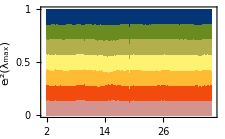

```mathematica
eigenVecFigRight=BarChart[(Map[(#^2&),(Abs@chosenFixedPointEigenvectors),{2}][[;;,-1]]),
Frame->True,
Axes->False,

FrameTicks->{{(*Automatic*){0,0.5,1},None},{Table[{((i-2)/34*239)+1,i},{i,Range[2,36,4]}],None}},


FrameTicksStyle->Directive[Black,FontSize->10,FontFamily->"Times"],
FrameStyle->Directive[Black],

FrameLabel->{Style[(*ToExpression["\\text{Time( h)}",TeXForm]*)"Time(h)",FontSize->12,FontFamily->"Times",Black],Style[ToExpression["e_{i}^2(\\lambda_{max})",TeXForm],FontSize->12,FontFamily->"Times",Black]},

(*PlotLabel->Style["B",Black,FontFamily->"Times",FontSize->12],*)

ImageSize->8 cm,
PlotRange->{{-3,243},{0,1}},

ImagePadding->{{37, 2}, {37, 1}},

ChartLayout->"Stacked",
ChartStyle->ColorData[14]
]
```

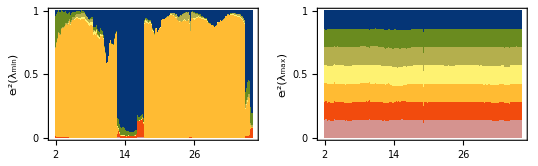

```mathematica
figfi=GraphicsRow[
{eigenVecFigLeft,
eigenVecFigRight},

Spacings->Scaled[0],
Alignment->Left,

ImageSize->19 cm,
ImagePadding->Automatic]
```

```mathematica
legendMarkerShapes=Table[Graphics[
{
{i[[1]],EdgeForm[Thickness[0.02]],Opacity[1],Rectangle[{0,0},{0.22,0.22},RoundingRadius->0.04]},
{Black,FontFamily->"Times",FontSize->8,Text[i[[2]],{0.82,0.11}]}
},
ImageSize->2cm,
ImagePadding->{{1,22},{1,1}}],
{i,MapThread[List,{Table[ColorData[14][i],{i,1,7}],{"FIN-AU  ","FIN-TTY ","NOR-NTUN","SWE-CTH ","SWE-KTH ","SWE-LTH ","SWE-LTU "}}]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.65,1.85}

```mathematica
graphicalLegendWithBackgrouond=Show[
Graphics[{White,EdgeForm[Thickness[0.01]],Opacity[1],Rectangle[{0,0},{3.5,5},RoundingRadius->0.2]}],
Epilog->{
Inset[legendMarkerShapes[[1]],Scaled[{0.5,0.11}],Automatic,Automatic],
Inset[legendMarkerShapes[[2]],Scaled[{0.5,0.24}],Automatic,Automatic],
Inset[legendMarkerShapes[[3]],Scaled[{0.5,0.37}],Automatic,Automatic],
Inset[legendMarkerShapes[[4]],Scaled[{0.5,0.5}],Automatic,Automatic],
Inset[legendMarkerShapes[[5]],Scaled[{0.5,0.63}],Automatic,Automatic],
Inset[legendMarkerShapes[[6]],Scaled[{0.5,0.76}],Automatic,Automatic],
Inset[legendMarkerShapes[[7]],Scaled[{0.5,0.89}],Automatic,Automatic]
},
ImageSize->2.15cm
]
```

-Graphics-

#### Fig. 3. (D)

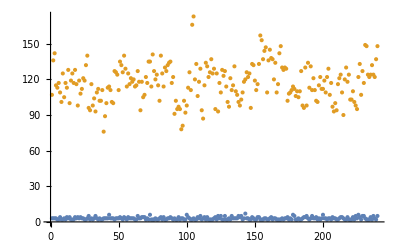

```mathematica
ListPlot[{(*FixedPointsWindows[[;;,1,1]],*)FixedPointsWindows[[;;,2,1]],FixedPointsWindows[[;;,3,1]]}]
```

#### Other Stable Fixed Points’ Values

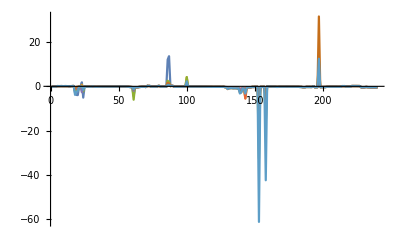

```mathematica
ListLinePlot[Transpose[FixedPointsWindows[[;;,2,3,1]]],PlotRange->All]
```

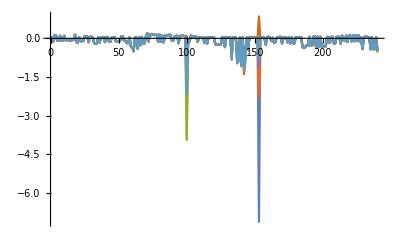

```mathematica
ListLinePlot[Transpose[FixedPointsWindows[[;;,2,3,2]]],PlotRange->All]
```

#### Fig. 3. (E) - The Chosen Fixed Point in Time

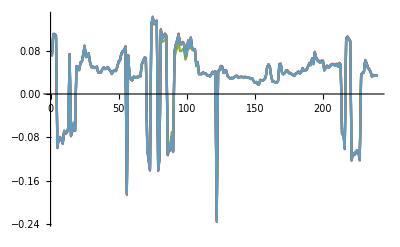

```mathematica
ListLinePlot[Transpose[FixedPointsWindows[[;;,2,3,-1]]],PlotRange->All]
```

#### Fig. 3. (F)

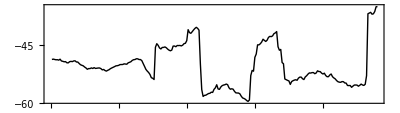

```mathematica
ListLinePlot[Re[FixedPointsWindows[[;;,2,2,-1,1]]],Frame->True,AspectRatio->1/3.5,PlotStyle->Directive[Black,Thick]]
```

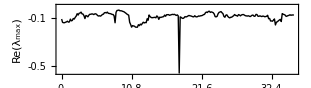

```mathematica
ListLinePlot[Re[FixedPointsWindows[[;;,2,2,-1,-1]]],
ImageSize->11 cm,
PlotRange->All,
PlotStyle->Directive[Black,Thick],
Frame->True,
AspectRatio->1/3.5,
FrameStyle->Directive[Black],
FrameTicks->{{{-0.5,-0.1},None},{Table[{i,Rotate[36/240*(i-1)//N,Pi/4]},{i,Range[1,240,18]}],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{Style[ToExpression["\\text{Time}",TeXForm],FontSize->12,FontFamily->"Times",Black],Style[ToExpression["\\text{Re}(\\lambda_{max})",TeXForm],FontSize->12,FontFamily->"Times",Black]}
]
```

#### Fig. 3. (H)

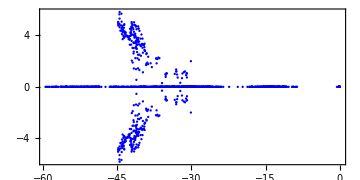

```mathematica
ComplexListPlot[FixedPointsWindows[[;;,2,2,-1,;;]],AspectRatio->1/2,PlotStyle->Directive[Blue,Large],Frame->True,ImageSize->Medium]
```